## Section | Beam Splitters and Interferometry

This chapter builds a quantum mechanical model of beam splitters and interferometers. We treat a lossless beam splitter as a two-port device that linearly maps input mode operators to output modes while preserving bosonic commutators. With this formalism we derive hallmark interference effects such as the Hong\[Dash]Ou\[Dash]Mandel bunching of indistinguishable photon pairs. The same tools analyze multi-element setups like the Mach\[Dash]Zehnder interferometer, where relative phase shifts convert path-length differences into measurable intensity fringes and detection probabilities. We also emphasize that even the \[OpenCurlyDoubleQuote]most classical\[CloseCurlyDoubleQuote] states of light retain quantum uncertainties, and we close with a brief discussion of polarization.

### Key concepts

Quantum description of beam-splitters

Mode transformation (Heisenberg evolution) and unitary evolution

Mach Zehnder Interferometer (MZI)

Wave- particle duality using single photons

Standard quantum limit

### Quantum Mechanical Description of Beam Splitters

Classically, a lossless beam splitter (BS) is modeled as a device with one input mode and two output modes, associated with transmitted and reflected amplitudes. That picture is not adequate in a fully quantum model because the commutation relations are not preserved:

.

A proper quantum description introduces an additional (often unused) port, whose field is in the vacuum state but still has physical consequences. With this extra mode the commutation relations hold, and we can analyze phenomena that have no classical explanation.

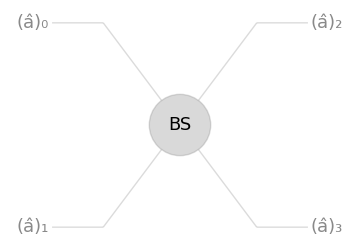
```mathematica
-Graphics--Graphics-
```

We therefore model the beam splitter as a device with two input modes and two output modes. The input and output creation operators are related by a linear transformation that depends on the complex reflection and transmission coefficients:

#### Types of Beam Splitters

A general beam-splitter matrix can be parameterized by a global phase and the reflection/transmission phases (ϕ_r, ϕ_t) and the reflectivity (θ):

Define a general beam-splitter:

```mathematica
GeneralBS = QuantumOperator[ⅇ^(ⅈ ϕg)({{Sin[θ] ⅇ^(ⅈ ϕr), Cos[θ] ⅇ^(-ⅈ ϕt)}, {Cos[θ] ⅇ^(ⅈ ϕt), -Sin[θ] ⅇ^(-ⅈ ϕr)}}),"Parameters"->{θ,ϕg,ϕr,ϕt}];
```

In practice, two beam-splitter types are most common: dielectric and symmetric. For a balanced 50:50 beam splitter set \[Theta] = π/4, and choose the remaining phases as specified below

Dielectric BS ; in the 50:50 case this becomes:

```mathematica
GeneralBS[π/4,0,0,0]
```

1/(√2)00+1/(√2)01+1/(√2)10-1/(√2)11

Symmetric BS ; in the 50:50 case this becomes:

```mathematica
GeneralBS[π/4,π/2,-π/2,0]
```

1/(√2)00+ⅈ/(√2)01+ⅈ/(√2)10+1/(√2)11

In general, in terms of the reflectivity r, we can write:

```mathematica
bs1 = GeneralBS[ArcSin[r],0,0,0];
```

The associated matrix is t =√(1-r^2):

```mathematica
Normal[(bs1["Matrix"])]/. √(1-r^2)->t//MatrixForm
```

(r | t
t | -r)

The beam-splitter evolution matrix is unitary:

```mathematica
FullSimplify[SuperDagger[bs1]@bs1,0<r<1]==QuantumOperator["I"]
```

True

### Digression: Polarization of a Photon

Photon polarization forms a two-level quantum system that mirrors the classical Jones-vector description.

Define the H/V basis:

```mathematica
polBasis = QuantumBasis[{"H","V"}];
```

An alternative basis is working in the diagonal and antidiagonal basis:

```mathematica
diagPolBasis =QuantumBasis@AssociationThread[{"D","A"}->QuantumBasis["X"]["Elements"]];
```

Change of basis in the Wolfram Quantum Framework:

```mathematica
QuantumState["+",polBasis]
QuantumState[%,diagPolBasis]
```

1/(√2)H+1/(√2)V

D

Example: Polarization projection

Project the first photon of the |ψ^-⟩ state onto diagonal polarization and plot the amplitudes in the two-photon diagonal/antidiagonal basis.

Create state:

```mathematica
psiminus = QuantumState["PsiMinus",polBasis]
```

1/(√2)HV-1/(√2)VH

Project the first photon (this means using a polarizer or projector |D⟩ ⟨D|):

```mathematica
projectionD =QuantumState["0",diagPolBasis]["Projector"]@QuantumState["PsiMinus",polBasis]
```

-1/2DH+1/2 DV

Use "AmplitudesPlot", only |DA⟩ nonzero amplitude:

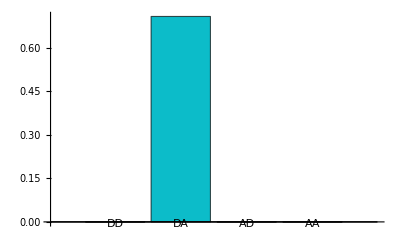

```mathematica
QuantumState[projectionD,QuantumBasis[{diagPolBasis,diagPolBasis}]]["AmplitudesPlot",ChartLegends->Automatic]
```

#### Wave plates

To rotate polarization, we use wave plates made of birefringent materials.

We define the half- and quarter-wave plates (HWP, QWP) in the H/V basis. To obtain the matrix at an angle \[Theta], rotate into the wave-plate frame, apply the \[Theta] = 0 matrix, and rotate back.

Half-wave plate at angle θ:

```mathematica
TraditionalForm[mat1=RotationMatrix[θ].{{1,0},{0,ⅇ^(ⅈ π)}}.RotationMatrix[-θ]//Simplify]
```

(cos(2 θ) | sin(2 θ)
sin(2 θ) | -cos(2 θ))

Quarter-wave plate at angle θ:

```mathematica
TraditionalForm[mat2 =RotationMatrix[θ].{{1,0},{0,ⅇ^(ⅈ π/2)}}.RotationMatrix[-θ]//Simplify]
```

(cos^2(θ)+ⅈ sin^2(θ) | (1-ⅈ) sin(θ) cos(θ)
(1-ⅈ) sin(θ) cos(θ) | sin^2(θ)+ⅈ cos^2(θ))

Wrap the matrices as QuantumOperator objects:

```mathematica
HWP = QuantumOperator[mat1,polBasis,"Parameters"->θ];
QWP = QuantumOperator[mat2,polBasis,"Parameters"->θ];
```

Common single-qubit gates correspond to particular wave-plate angles:

```mathematica
HWP[π/4]==QuantumOperator["X"]
```

True

```mathematica
HWP[π/8]==QuantumOperator["H"]
```

True

Transforming |H⟩ polarization to |V⟩:

```mathematica
HWP[π/4][]
```

V

In general, any SU(2) operator on polarization can be realized with a sequence of QWP-HWP-QWP operations.

### Evolution of Quantum States in Beam Splitters

Define the output modes:

```mathematica
{a2,a3} = Table[AnnihilationOperator[{i}],{i,2}];
```

We use a symmetric 50:50 beam splitter:

```mathematica
balancedBS =GeneralBS[π/4,π/2,-π/2,0];
```

We use the inverse matrix because we are expressing input modes in terms of output modes (a Heisenberg-picture evolution):

```mathematica
{a0,a1} = Inverse@balancedBS["Matrix"].{a2,a3};
```

Evolution of the one-photon state :

```mathematica
onePhotonEvolve = SuperDagger[a1][]
```

1/(√2)01+ⅈ/(√2)10

The output state is entangled; see QuantumEntanglementMonotone (default metric: \[OpenCurlyDoubleQuote]Concurrence\[CloseCurlyDoubleQuote]):

```mathematica
QuantumEntanglementMonotone[onePhotonEvolve,{1,2}]
```

1

If we inject one photon into each input port, the photons emerge together in the same output. This bunching arises from two-photon interference when the photons are indistinguishable (Hong\[Dash]Ou\[Dash]Mandel effect).

State will evolve as :

```mathematica
twoPhotonEvolve = SuperDagger[a0]@SuperDagger[a1][]
```

ⅈ/(√2)02+ⅈ/(√2)20

We can also adopt a Schrodinger-picture description; for a symmetric 50:50 beam splitter the unitary is

Define the modes:

```mathematica
{a0,a1} = Table[AnnihilationOperator[{i}],{i,2}];
```

Compute the unitary operator representing the beam splitter:

```mathematica
U = QuantumOperator[MatrixExp[ⅈ π/4.(SuperDagger[a0]@a1+a0@SuperDagger[a1])],"Label"->"BS"];
```

Represent the evolution as a circuit:

```mathematica
photonEvolve = QuantumCircuitOperator[{FockState[{1,1}],U}];
```

See the diagram:

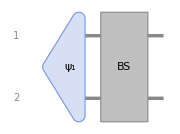

```mathematica
photonEvolve["Diagram",ImageSize->Small]
```

Schrodinger-picture evolution:

```mathematica
Chop[photonEvolve[]]
```

(0.+0.707107 ⅈ)02+(0.+0.707107 ⅈ)20

In the QuantumFramework we have  BeamSplitterOperator for doing Schrodinger picture evolution (recurrence method is preferred for symbolic numbers)

```mathematica
balancedsymmetric = BeamSplitterOperator[{π/4,π/2},Method->"Recurrence"];
```

We get the same result:

```mathematica
balancedsymmetric@FockState[{1,1}]
```

ⅈ/(√2)02+ⅈ/(√2)20

Now place a coherent state in input port 1,  , and evolve it using

Numerical amplitudes:

```mathematica
αcoh = RandomReal[{1,1.5}]Exp[ⅈ RandomReal[{0,2π}]];
```

Evolve the operators:

```mathematica
{a0,a1} = Inverse@balancedBS["Matrix"].{a2,a3};
```

Output state:

```mathematica
cohBS = MatrixExp[(αcoh a1["Dagger"]-αcoh* a1)][]//Chop;
```

The entanglement monotone is essentially zero, so the state is a product (not entangled):

```mathematica
QuantumEntanglementMonotone[cohBS,{{1},{2}}]
```

0.

The analytic result shows that a coherent state behaves like a classical field at a 50:50 BS: the mean photon number is |α|^2/2 in each output mode and a phase shift π/2 for the reflected wave.

Product state:

```mathematica
productState = coherent[ⅈ αcoh/√2] //coherent[αcoh/√2];
```

Evaluate how similar the states are, should be really close to 1:

```mathematica
QuantumSimilarity[cohBS,productState,"Fidelity"]
```

1.

Individual amplitudes have numerical error though, the ones that have bigger numerical error are mostly related to the edge effects of truncation:

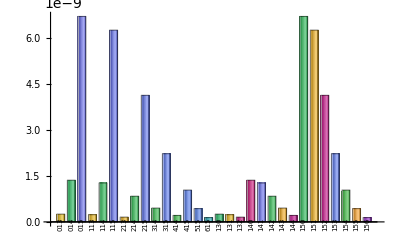

```mathematica
(productState-cohBS)["AmplitudePlot",]
```

More generally, the beam splitter transforms an input Fock state so that N photons are binomially distributed between the two modes.

Let’s verify that for a particular N:

```mathematica
Np = 8;
```

Output state:

```mathematica
outstate = balancedsymmetric[FockState[{0,Np}]]
```

1/16 08+ⅈ/(4 √2)17-(√7)/826-1/4 ⅈ √(7/2)35+(√(35/2))/8 44+1/4 ⅈ √(7/2)53-(√7)/862-ⅈ/(4 √2)71+1/16 80

Probability plot of the output state:

```mathematica
p1 =outstate["ProbabilityPlot",AxesLabel->{"States","Probability"}];
```

Binomial distribution with parameters N_p and p = 0.5:

```mathematica
p2=DiscretePlot[PDF[BinomialDistribution[Np,0.5],k-1],{k,1,Np+1},PlotStyle->{Black,PointSize[0.015]}];
```

Show the result:

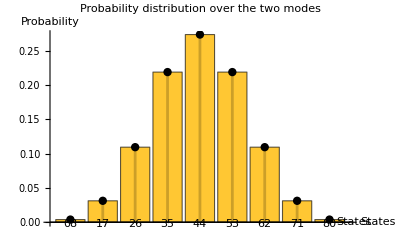

```mathematica
Show[p1,p2,PlotLabel->"Probability distribution over the two modes",ImageSize->400,LabelStyle->12]
```

### Single-Photon Mach–Zehnder Interferometer

Let\[CloseCurlyQuote]s consider the single-photon Mach\[Dash]Zehnder interferometer. It consists of two beam splitters and a phase shift in one arm. The arrangement is shown below:

Set up a small truncation size:

```mathematica
SetFockSpaceSize[3];
```

Now we use a dielectric beam-splitter:

```mathematica
dielectricBS = QuantumOperator[BeamSplitterOperator[{π/4,0}],"Label"->"BS"];
```

Phase shift operator:

```mathematica
phase = QuantumOperator[PhaseShiftOperator[ϕ],"Label"->"ϕ"];
```

Circuit representation of the Mach-Zehnder interferometer arrangement:

```mathematica
MZI =QuantumCircuitOperator[{dielectricBS,phase,dielectricBS}];
```

See the diagram:

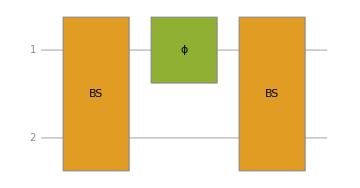

```mathematica
MZI["Diagram","GateBackgroundStyle"->]
```

Calculate the output probabilities:

```mathematica
probs =List@@MZI[FockState[{0,1}]]["Probability"]
```

{(Abs[1/2-ⅇ^(ⅈ ϕ)/2]^2)/(Abs[1/2-ⅇ^(ⅈ ϕ)/2]^2+Abs[-1/2-ⅇ^(ⅈ ϕ)/2]^2),(Abs[-1/2-ⅇ^(ⅈ ϕ)/2]^2)/(Abs[1/2-ⅇ^(ⅈ ϕ)/2]^2+Abs[-1/2-ⅇ^(ⅈ ϕ)/2]^2)}

Simplified probabilities:

```mathematica
simplifiedProbs =Simplify[ComplexExpand[probs],ϕ∈Reals]//TrigReduce
```

{1/2 (1-cos(ϕ)),1/2 (cos(ϕ)+1)}

Plotting probabilities at the detectors:

```mathematica
Plot[Evaluate@MapThread[Callout[#1,#2,Right]&,{simplifiedProbs,{"D1","D2"}}],{ϕ,0,6Pi},
]
```

-Graphics-

Experimentally, this illustrates wave\[Dash]particle duality: wave-like behavior appears in the interference fringes, while particle-like behavior appears as discrete detector clicks. The pattern builds up gradually as many individual photons pass through the interferometer.

### Interference of coherent states

Let\[CloseCurlyQuote]s analyze coherent-state interferometry in a Mach\[Dash]Zehnder interferometer. We expect results analogous to classical light, and we will follow a Schrodinger-picture evolution.

Set up the parameters:

```mathematica
SetFockSpaceSize[30];
αcoh = 1.8Exp[I RandomReal[{0,2Pi}]];
```

Balanced symmetric BS:

```mathematica
balancedsymmetric = BeamSplitterOperator[{π/4.,π/2.},Method->"Recurrence"];
```

MZI interferometer operator (phase shift θ in second arm):

```mathematica
MZI =balancedsymmetric@PhaseShiftOperator[θ,{2}]@balancedsymmetric;
```

Initial state:

```mathematica
init = FockState[0]//coherent[αcoh];
```

Output state:

```mathematica
out = QuantumState[MZI[init],"Parameters"->θ];
```

Evidently the resulting state is a product state, zero entanglement monotone:

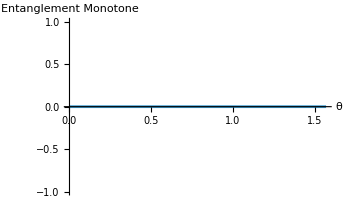

```mathematica
Plot[QuantumEntanglementMonotone[out[θ],{{1},{2}},"Concurrence"],{θ,0,π/2},AxesLabel->{"θ","Entanglement Monotone"}]
```

The analytic expression for the evolution is:

.

Product state analytical:

```mathematica
product = QuantumState[(coherent[(ⅈ(1+ⅇ^(ⅈ θ))αcoh)/2]//coherent[(( ⅇ^(ⅈ θ)-1)αcoh)/2]),"Parameters"->θ];
```

Sample phases:

```mathematica
phases = N@Subdivide[0,π/2,25];
```

Compare results, empty “AmplitudeList” represent states are numerically the same up the chosen precision:

```mathematica
Chop[(out[#]-product[#]),10^-9]["AmplitudeList"]&/@phases
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

The phase shift θ can be estimated by subtracting the intensities at two detectors, D_1 and D_2. This corresponds to the expectation value \[LeftAngleBracket]Ô ⟩ with Ô=c^†c-d^†d the number-difference operator for the output modes (c and d). This is straightforward to compute because, for a coherent state, the mean photon number equals the squared magnitude of the complex amplitude:

Output modes:

```mathematica
{c,d}= Array[AnnihilationOperator[{#}]&,2];
```

Current operator:

```mathematica
Ocurrent = SuperDagger[c]@c -SuperDagger[d]@d;
```

We can compute the mean of the Ô operator symbolically for each coherent state:

```mathematica
OmeanSymbolic = FullSimplify[Abs[(ⅈ (ⅇ^(ⅈ θ)+1)α)/2]^2-Abs[((ⅇ^(ⅈ θ)-1)α)/2]^2,Element[θ,Reals]]
```

α Conjugate[α] cos(θ)

Current expectations for varying phases θ:

```mathematica
currentMean =Simplify[Chop[(SuperDagger[out[θ]]@Ocurrent@out[θ])["Scalar"]],θ∈Reals];
```

From the symbolic expression we can recover \[Theta]; this simply demonstrates the equivalence computationally, while real measurements are affected by noise and finite precision:

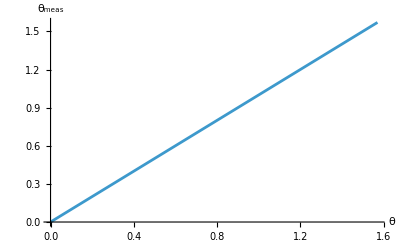

```mathematica
Plot[ArcCos[{Re@currentMean}/Abs[αcoh]^2],{θ,0,π/2},AxesLabel->{"θ"," θ_meas"}]
```

The result matches the classical prediction for coherent light, but coherent states are still quantum and exhibit fluctuations. Using error propagation, the phase-estimation uncertainty is

,

This uncertainty is minimized at odd multiples of \[Pi]/2. That is the standard quantum limit for classical-like states. Non-classical light can beat this limit; one example is its use in large-scale gravitational-wave interferometers (LIGO).

### Fock space and polarization joint basis

To represent a truncated Fock space with polarization, specify the two occupation numbers n_H and n_V for horizontal and vertical polarizations. The vacuum corresponds to n_H=0 and n_V=0

Define an occupation-number basis for a chosen polarization:

```mathematica
PolarizationNBasis[size_:$FockSize,pol_]:=QuantumBasis@Table[StringTemplate["\!\(\*SubscriptBox[\(`n`\), \(`pol`\)]\)"][Association["n"->n,"pol"->pol]],{n,0,size-1}]
```

Show the basis states:

```mathematica
PolarizationNBasis[3,H]["Association"]//Keys
```

{0_H,1_H,2_H}

If we cap the total photon number at n, the joint polarization basis has dimension ((n + 1)(n + 2))/2; here size is n+1 (to include 0):

```mathematica
FockPolarizationBasis[size_:$FockSize]:=QuantumBasis@Flatten@Table[StringTemplate["\!\(\*SubscriptBox[\(`nH`\), \(H\)]\)\!\(\*SubscriptBox[\(`nV`\), \(V\)]\)"][<|"nH"->nH,"nV"->nV|>],{nH,0,size-1},{nV,0,size-1-nH}]
```

List the basis states for a chosen size:

```mathematica
FockPolarizationBasis[4]["Association"]//Keys
```

{0_H0_V,0_H1_V,0_H2_V,0_H3_V,1_H0_V,1_H1_V,1_H2_V,2_H0_V,2_H1_V,3_H0_V}

Define a helper function that returns valid occupation-number pairs:

```mathematica
basisPairs[size_]:=Flatten[Table[{nH,nV},{nH,0,size-1},{nV,0,size-nH-1}],1];
```

Implement the polarization-resolved annihilation operator:

```mathematica
AnnihilationOperatorPolarization[size_:$FockSize,pol_]:=Block[{pairs=basisPairs[size],dim,index,rules},dim=Length[pairs];
index=AssociationThread[pairs->Range[dim]];
rules=Flatten[MapIndexed[With[{nH=#[[1]],nV=#[[2]],i=First[#2]},
Which[
pol==="H"&&nH>=1,
{{index[{nH-1,nV}],i}->Sqrt[nH]},
pol==="V"&&nV>=1,
{{index[{nH,nV-1}],i}->Sqrt[nV]},
True,{}]]&,pairs]];
QuantumOperator[SparseArray[rules,{dim,dim}],FockPolarizationBasis[size]]]
```

Inspect the represented states:

```mathematica
FockPolarizationBasis[4]["Association"]//Keys
```

{0_H0_V,0_H1_V,0_H2_V,0_H3_V,1_H0_V,1_H1_V,1_H2_V,2_H0_V,2_H1_V,3_H0_V}

Annihilation operators for horizontal and vertical polarizations:

```mathematica
aH := AnnihilationOperatorPolarization["H"]
aV := AnnihilationOperatorPolarization["V"]
```

Test the vacuum state:

```mathematica
vacuum = QuantumState["0",FockPolarizationBasis[]]
```

0_H0_V

```mathematica
aH@vacuum
```

0

Test the state a_V|0_H,1_V\[RightAngleBracket]:

```mathematica
QuantumState["1",FockPolarizationBasis[]]
```

0_H1_V

```mathematica
aV@%
```

0_H0_V

A one-photon state with diagonal polarization can be represented as:

```mathematica
1/(√2)(SuperDagger[aH]+SuperDagger[aV])[]
```

1/(√2)0_H1_V+1/(√2)1_H0_V

##### Initialization

Load the Quantum Framework:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load the second quantization tools:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Useful definitions:

```mathematica
a := AnnihilationOperator[]
coherent := CoherentState[]["Normalize"]
```

Vocabulary

BeamSplitterOperator |   | Operator  that performs evolution of states going
through a beam-splitter in the Schrodinger picture
PhaseShiftOperator |   | Applies a phase factor proportional to the photon number
of the Fock state
QuantumEntanglementMonotone |   | calculates a metric to measure entanglement of a
QuantumState, default metric is “Concurrence”

Exercises

Define the basis of circular right |R⟩, and circular left polarization |L⟩ (use any convention):

Solution

QuantumBasis@AssociationThread[{"R","L"}->QuantumBasis["Y"]["Elements"]]

<|"R"→{1/(√2),ⅈ/(√2)},"L"→{1/(√2),-ⅈ/(√2)}|>

Or:

QuantumBasis[<|"R"->1/(√2){1, ⅈ},"L"->1/(√2){1,-ⅈ}|>]

<|"R"→{1/(√2),ⅈ/(√2)},"L"→{1/(√2),-ⅈ/(√2)}|>

Check that the state |3,1⟩ has a uniform distribution after a balanced beam-splitter operation

Solution

BeamSplitterOperator[{π/4.,π/2.}][FockState[{3,1}]]["ProbabilityPlot"]

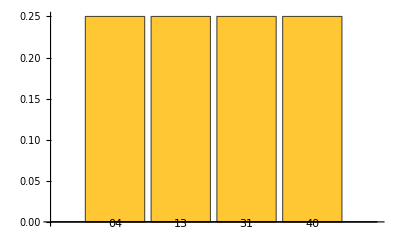

Given the generators 
J_1=1/2(a_0^†a_1+a_1^†a_0),  J_2= 1/2 ⅈ (a_0^†a_1-a_1^†a_0),   J_3=1/2((a^†)_0 a_0-(a^†)_1 a_1)
these generators can describe beam-splitter transformations constructing the unitary
 U(θ) = exp(ⅈ θ J_i). Show the generators satisfy the angular momentum algebra [J_i,J_j] = ⅈ ε_(i j k) J_k.
If we define J_0=1/2(a_0^†a_0+a_1^†a_1) show J_0 commutes with all the generators, and check J^2 = J_0(J_0+1)

Solution

Define the J_i operators:

J0 = (a0^†**a0+a1^†**a1)/2;
JList ={(a0^†**a1+a1^†**a0)/2,(a0^†**a1-a1^†**a0)/(2ⅈ),(a0^†**a0-a1^†**a1)/2};

Define all the commutation relations for two modes and the non-commutative variables:

rels = {Commutator[a0,a0^†]-1,Commutator[a1,a1^†]-1, Commutator[a0,a1],Commutator[a0^†,a1^†],Commutator[a0^†,a1],Commutator[a0,a1^†]};

vars = {a0,a1,a0^†,a1^†};

Verify the angular momentum algebra:

resComm=Table[NonCommutativePolynomialReduce[Commutator[JList[[i]],JList[[j]]]-I*Sum[Signature[{i,j,k}]*JList[[k]],{k,3}],rels,vars][[-1]],{i,3},{j,3}]//MatrixForm

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

J_0 commutes with all the generators:

```mathematica
Table[NonCommutativePolynomialReduce[Commutator[J0,JList[[i]]],rels,vars][[-1]],{i,3}]
```

{0,0,0}

Verify the relation J^2=J_0(J_0+1):

NonCommutativePolynomialReduce[Sum[Ji**Ji,{Ji,JList}]-J0**(J0+1),rels,vars][[-1]]

0

A polarizing beam-splitter (PBS) is a device that also has two spatial input and output modes but that is sensitive to polarization. Horizontal polarization is transmitted and vertical polarization is reflected, for single photons the PBS can be described in 4-dimensional Hilbert space. Define the QuantumOperator representing the PBS, assume we have diagonal polarization incoming in one input mode , then show the state after the PBS is unpolarized (mixed)

Solution

Define polarization basis:

polBasis = QuantumBasis[{"H","V"}];

Define path basis:

pathBasis = QuantumBasis[{"e_0","e_1"}];

It can be derived that the associated matrix in the joint basis is very similar to a CNOT gate, horizontal polarization keeps the path label but vertical polarization flips it:

PBS = QuantumOperator[(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),{polBasis,pathBasis}]

"H""e_0""H""e_0"+"H""e_1""H""e_1"+ⅈ"V""e_0""V""e_1"+ⅈ"V""e_1""V""e_0"

We get the expected result ρ_pol=1/2(1 | 0
0 | 1):

QuantumPartialTrace[PBS[QuantumState["+",polBasis]//QuantumState["0",pathBasis]],{2}]==QuantumState["UniformMixture",polBasis]

True

Using a balanced beam splitter obtained with J_1 generator, show numerically(for some value of N) that for an input state |N⟩|N⟩ the output state takes the form
|out⟩ = (ⅈ)^N(∑^N)_(k = 0) (Binomial[2k,k] Binomial[2N-2k,N-k] (1/2)^(2N))^(1/2) |2k⟩ |2N - 2k⟩
Do a plot of the joint photon distribution for non zero values

Solution

Define a value of truncation, the value of N and the operators:

SetFockSpaceSize[16];
Np=($FockSize-2)/2;

a0 := AnnihilationOperator[];
a1 := AnnihilationOperator[{2}];

Building the beam-splitter operator:

BSJ1 =MatrixExp[ ⅈ π/2.(a0^†@a1+a0@a1^†)/2];

Output states corresponding to the evolution and the analytical expression:

outState =Chop[BSJ1[FockState[{Np,Np}]]]

(0.-0.457682 ⅈ)014+(0.-0.335847 ⅈ)212+(0.-0.303785 ⅈ)410+(0.-0.292317 ⅈ)68+(0.-0.292317 ⅈ)86+(0.-0.303785 ⅈ)104+(0.-0.335847 ⅈ)122+(0.-0.457682 ⅈ)140

analytic =((ⅈ)^Np Sum[√(Binomial[2k,k]Binomial[2Np-2k,Np-k](1/2.)^(2 Np))FockState[{2k,2Np-2k}],{k,0,Np}])

(0.-0.457682 ⅈ)014+(0.-0.335847 ⅈ)212+(0.-0.303785 ⅈ)410+(0.-0.292317 ⅈ)68+(0.-0.292317 ⅈ)86+(0.-0.303785 ⅈ)104+(0.-0.335847 ⅈ)122+(0.-0.457682 ⅈ)140

Show the probability distribution:

outState["ProbabilityPlot"]

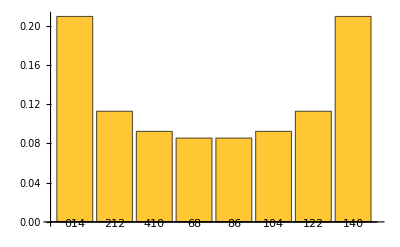

In the limit of N big, the distribution takes the form of the arcsine distribution (up to some scaling):

Plot[PDF[ArcSinDistribution[],x],{x,0,1},PlotRange->{0,2}]